```mathematica
Pr0=.72;Ra=10^5;R=Ra*Pr0;t0=1/100;a=0;
Ω=ImplicitRegion[0≤x≤1&&0≤y≤1,{x,y}];

{UX,VY,Ρ,TK,TX}=NDSolveValue[{{({{-μ,0},{0,-μ}}.u[x,y]{x,y}Inactive){x,y}Inactive+D[p[x,y],x]+u[x,y]*D[u[x,y],x]+v[x,y]*D[u[x,y],y]-R*T[x,y]*Sin[a],({{-μ,0},{0,-μ}}.v[x,y]{x,y}Inactive){x,y}Inactive+D[p[x,y],y]+u[x,y]*D[v[x,y],x]+v[x,y]*D[v[x,y],y]-R*T[x,y]*Cos[a],D[u[x,y],x]+D[v[x,y],y]}=={0,0,0}/.μ->Pr0,{
DirichletCondition[{p[x,y]==0},y==1&&x==1],DirichletCondition[{u[x,y]==0,v[x,y]==0},y==0||y==1]},{u[x,y]*D[T[x,y],x]+v[x,y]*D[T[x,y],y]-(D[T[x,y],x,x]+D[T[x,y],y,y])==NeumannValue[0,y==0||y==1],DirichletCondition[{u[x,y]==0,v[x,y]==0,T[x,y]==1},x==0],DirichletCondition[{u[x,y]==0,v[x,y]==0,T[x,y]==0},x==1]}},{u,v,p,T,Derivative[1,0][T]},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1,T->2},"MeshOptions"->{"MaxCellMeasure"->0.0001}}];
```

```mathematica
MaximalBy[Table[{x,VY[x,.5]},{x,0,1,.0001}],Last]
```

{{0.066,68.7316}}

```mathematica
(*BenchmarkCase={x=0.066,vmax=68.59}*)
```

```mathematica
MaximalBy[Table[{y,UX[0.5,y]},{y,0,1,.0001}],Last]
```

{{0.8543,34.6607}}

```mathematica
(*BenchmarkCase={y=0.855,umax=34.73}*)
```

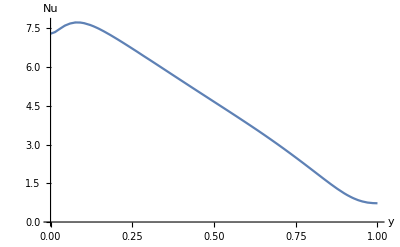

```mathematica
Plot[-TX[0,y],{y,0,1},AxesLabel->{"y","Nu"}]
```

```mathematica
MaximalBy[Table[{y,-TX[0,y]},{y,0,1,0.0001}],Last]
```

{{0.0747,7.73417}}

```mathematica
(*BenchmarkCase={y=0.081,Numax=7.717}*)
```

```mathematica
NuAv=NIntegrate[UX[x,y]*TK[x,y]-TX[x,y],{x,0,1},{y,0,1},WorkingPrecision->5]
```

4.488

```mathematica
(*BenchmarkCase=4.519*)
```

```mathematica
Nu0=NIntegrate[-TX[0,y],{y,0,1},WorkingPrecision->5]
```

4.5274

```mathematica
(*BenchmarkCase=4.509*)
```

```mathematica
Nu05=NIntegrate[UX[.5,y]*TK[.5,y]-TX[0.5,y],{y,0,1},WorkingPrecision->5]
```

4.5252

```mathematica
(*BenchmarkCase=4.519*)

MinimalBy[Table[{y,-TX[0,y]},{y,0,1,0.0001}],Last]
```

{{1.,0.726786}}

```mathematica
(*BenchmarkCase={y=1,Numin=0.729}*)
```

```mathematica
(*Vahl Davis,G.de (1983):Natural convection of air in a square cavity:A bench mark numerical solution.Int.J.Numer.Methods Fluids 3,249–264*)
```

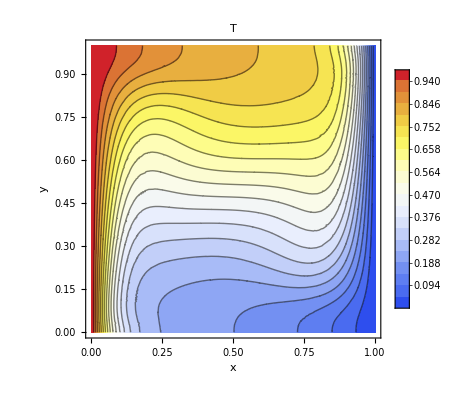
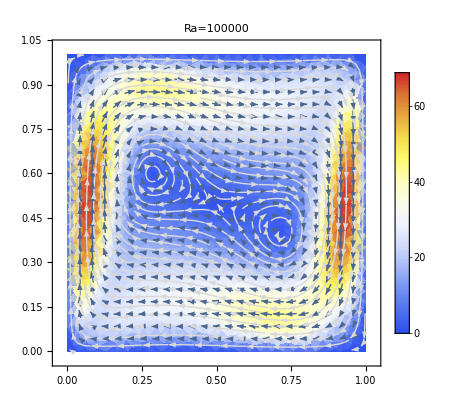

```mathematica
{ContourPlot[TK[x,y],{x,y}∈Ω,PlotLegends->Automatic,Contours->20,PlotPoints->25,ColorFunction->"TemperatureMap",AxesLabel->{"x","y"},PlotLabel->T],StreamDensityPlot[{UX[x,y],VY[x,y]},{x,y}∈Ω,StreamPoints->Fine,StreamStyle->LightGray,PlotLegends->Automatic,VectorPoints->Fine,ColorFunction->"TemperatureMap",PlotLabel->Row[{"Ra=",Ra}]]}
```